```mathematica
tab = Table[i j k , {i , 1 , 2} , {j , 1 , 4} , {k , 1 , 3}];
```

```mathematica
tab
```

{{{1,2,3},{2,4,6},{3,6,9},{4,8,12}},{{2,4,6},{4,8,12},{6,12,18},{8,16,24}}}

```mathematica
Length[tab]
```

2

```mathematica
Dimensions[tab]
```

{2,4,3}

```mathematica
{{1 , 2} , {1 , 2 , 3 , {4 , 5}}}//Dimensions
```

{2}

```mathematica
f/@{a , b , c}
```

{f[a],f[b],f[c]}

```mathematica
Hold[FullForm[f/@{a , b , c}]]
```

Hold[Map[f,List[a,b,c]]]

```mathematica
?Map
```

```mathematica
m = {{1 , 2 ,3} , {4 , 5 , 6} , {7 , 8 , 9}};
```

```mathematica
m//MatrixForm
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

```mathematica
Function[x , x^2]/@{1 , 2 , 3}
```

{1,4,9}

```mathematica
fun/@m
```

{fun[{1,2,3}],fun[{4,5,6}],fun[{7,8,9}]}

```mathematica
Map[fun , m , {2}]//MatrixForm
```

(fun[1] | fun[2] | fun[3]
fun[4] | fun[5] | fun[6]
fun[7] | fun[8] | fun[9])

```mathematica
?Inner
```

```mathematica
Inner[f , {1 ,2} , {3 , 4} , g]
```

g[f[1,3],f[2,4]]

```mathematica
{1 , 2} .{3 , 4}
```

11

```mathematica
Inner[Function[{x , y} , x y] , {1 ,2} , {3 , 4} , Function[{x , y} , x+y]]
```

11

```mathematica
?Accumulate
```

```mathematica
Accumulate[{1 , 2 , 3 , 4}]
```

{1,3,6,10}

```mathematica
tab
```

{{{1,2,3},{2,4,6},{3,6,9},{4,8,12}},{{2,4,6},{4,8,12},{6,12,18},{8,16,24}}}

```mathematica
Flatten[tab]
```

{1,2,3,2,4,6,3,6,9,4,8,12,2,4,6,4,8,12,6,12,18,8,16,24}

```mathematica
Dimensions[tab]
```

{2,4,3}

```mathematica
ArrayReshape[Flatten[tab] , {2 , 4 , 3}]
```

{{{1,2,3},{2,4,6},{3,6,9},{4,8,12}},{{2,4,6},{4,8,12},{6,12,18},{8,16,24}}}

```mathematica
f/@Partition[Riffle[{"a" , "b" , "c"} , {1 , 2 , 3}] , 2]
```

{f[{a,1}],f[{b,2}],f[{c,3}]}

```mathematica
m//MatrixForm
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

```mathematica
m//Transpose//MatrixForm
```

(1 | 4 | 7
2 | 5 | 8
3 | 6 | 9)

```mathematica
?MapIndexed
```

```mathematica
MapIndexed[f , {"a" , "b" , "c"}]
```

{f[a,{1}],f[b,{2}],f[c,{3}]}

```mathematica
MapIndexed[f , {{"a" , "b" , "c"} , {"d" , "e" , "f"}} , {2}]
```

{{f[a,{1,1}],f[b,{1,2}],f[c,{1,3}]},{f[d,{2,1}],f[e,{2,2}],f[f,{2,3}]}}

```mathematica
{{"a" , "b" , "c"} , {"d" , "e" , "f"}}[[2,2]]
```

e

```mathematica
mathematicaLogo = Import["/home/kacper/Pictures/banner-mathematica.png"]
```

-Graphics-

```mathematica
mathematicaLogoBW = ColorConvert[mathematicaLogo , "Grayscale"]
```

-Graphics-

```mathematica
mathematicaLogoBWData = ImageData[mathematicaLogoBW];
```

```mathematica
mathematicaLogoBWData//Dimensions
```

{319,290}

```mathematica
mathematicaLogoBWData//Head
```

List

```mathematica
mathematicaLogoBWData[[1,1]]
```

0.87451

```mathematica
Image[mathematicaLogoBWData]
```

-Graphics-

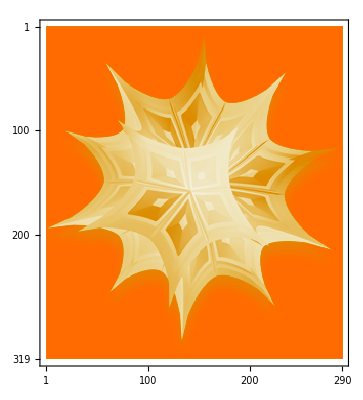

```mathematica
mathematicaLogoBWData//MatrixPlot
```

```mathematica
Sort
```

Sort

```mathematica
?Sort
```

```mathematica
?ListConvolve
```

```mathematica
?StandardDeviation
```

```mathematica
ListConvolve[{0.5 , 0.5},{1 , 2 , 3 , 4 , 5 , 6 ,7}]
```

{1.5,2.5,3.5,4.5,5.5,6.5}

```mathematica
{{0.25 , 0.25} , {0.25 , 0.25}}//MatrixForm
```

(0.25 | 0.25
0.25 | 0.25)

```mathematica
Image[ListConvolve[{{0.25 , 0.25} , {0.25 , 0.25}} , mathematicaLogoBWData]]
```

-Graphics-

```mathematica
Image[ListConvolve[Table[N[1/(50 50)] , {50} , {50}] , mathematicaLogoBWData]]
```

-Graphics-